# Illustration of harmonic spectrum

#### Cross section with v_1

```mathematica
f1[ϕ_,v1_,ψ1_]:=1/(2π)(1+2 v1 Cos[ϕ-ψ1])
```

```mathematica
Manipulate[
ParametricPlot[f1[ϕ,v1,ψ1]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π}],
{v1,0,1},{ψ1,0,2π,π/4}
]
```

#### Calculate v_n from cross section by definition

```mathematica
FNvnx[f_,n_]:=NIntegrate[f[ϕ]Cos[n ϕ],{ϕ,0,2π}]
FNvny[f_,n_]:=NIntegrate[f[ϕ]Sin[n ϕ],{ϕ,0,2π}]
```

```mathematica
n=1;
ψn=.1;
vnx=NIntegrate[f1[ϕ,1,ψn]Cos[n ϕ],{ϕ,0,2π}]
vny=NIntegrate[f1[ϕ,1,ψn]Sin[n ϕ],{ϕ,0,2π}]
Sqrt[vnx^2+vny^2]
```

0.995004

0.0998334

1.

#### Cross section with v_n

```mathematica
FNfn[ϕ_,vn_,ψn_,n_]:=1/(2π)(1+2 vn Cos[n(ϕ-ψn)]);
FNfnnorm[vn_,ψn_,n_]:=NIntegrate[FNfn[ϕ,vn,ψn,n],{ϕ,0,2π}];
FNfnScaled[ϕ_,vn_,ψn_,n_]:=FNfn[ϕ,vn,ψn,n]/FNfnnorm[vn,ψn,n];
```

```mathematica
n=2;
ψn=.1;
vn=.2;
vnx=NIntegrate[FNfnScaled[ϕ,vn,ψn,n]Cos[n ϕ],{ϕ,0,2π}]
vny=NIntegrate[FNfnScaled[ϕ,vn,ψn,n]Sin[n ϕ],{ϕ,0,2π}]
Sqrt[vnx^2+vny^2]/vn
{ArcTan[vny/vnx],(ψn n),ψn+π/2}
```

0.196013

0.0397339

1.

{0.2,0.2,1.6708}

```mathematica
Manipulate[
ParametricPlot[FNfn[ϕ,v1,ψ1,2]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π}],
{v1,0,1},{ψ1,0,π,π/4}
]
```

```mathematica
Manipulate[
ParametricPlot[FNfn[ϕ,v1,ψ1,3]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π}],
{v1,0,1},{ψ1,0,2π/3,π/3}
]
```

```mathematica
Manipulate[
ParametricPlot[FNfn[ϕ,v1,ψ1,4]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π}],
{v1,0,1},{ψ1,0,2π/4,π/4}
]
```

```mathematica
Manipulate[
ParametricPlot[FNfn[ϕ,v1,ψ1,5]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π}],
{v1,0,1},{ψ1,0,2π/5,π/5}
]
```

#### Styled plot v_n

```mathematica
glabelFN=(Style[#,FontFamily->"Times New Roman",16,Black]&);
```

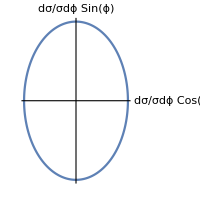
-Graphics-Style[dσ/dϕ=σ/(2  π),fontsizeL,FontFamily→font1,myBlue]

```mathematica
With[{v1=0,ψ1=0},
fig=ParametricPlot[
FNfn[ϕ,v1,ψ1,2]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},
ImageSize->200,
Ticks->None,
AxesLabel->glabelFN/@{"dσ/σdϕ Cos(ϕ)","dσ/σdϕ Sin(ϕ)"},
AxesStyle->Directive[Black]
];
Labeled[fig,Style["dσ/dϕ=σ/(2  π)",fontsizeL,FontFamily->font1,myBlue],Top]
]
```

```mathematica
With[{vn=0.3,ψn=π/3,n=1},
vnx=NIntegrate[FNfnScaled[ϕ,vn,ψn,n]Cos[n ϕ],{ϕ,0,2π}];
vny=NIntegrate[FNfnScaled[ϕ,vn,ψn,n]Sin[n ϕ],{ϕ,0,2π}];
fig=Show[
ParametricPlot[
FNfn[ϕ,vn,ψn,n]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},
ImageSize->200,
Ticks->None,
AxesLabel->glabelFN/@{"dσ/σdϕ Cos(ϕ)","dσ/σdϕ Sin(ϕ)"},
AxesStyle->Directive[Black],
Epilog->{Inset[Style["(v⃗)_1",fontsizeM+1,FontFamily->font1,myRed],Scaled[{.55,.8}]],
Inset[Style["ψ_1",fontsizeM,FontFamily->font1,myRed],Scaled[{.6,.4}]]
}
],
Graphics[{myRed,Arrowheads[Medium],Arrow[{{0,0},{vnx,vny}}]}],
Graphics[{myRed,Arrow[BSplineCurve[Table[{Cos[x],Sin[x]}vn/π/2,{x,0,ψn,ψn/10}]]]}]
];
Labeled[fig,Style[TraditionalForm["dσ/dϕ=σ/(2  π)[1+2v_1Cos(ϕ-ψ_1)]"],fontsizeL,FontFamily->font1,myBlue],Top]
]
```

-Graphics-dσ/dϕ=σ/(2  π)[1+2v_1Cos(ϕ-ψ_1)]

```mathematica
myRed=Red;
fontsizeM=16;
font1="Times"
```

Times

```mathematica
FNfn[ϕ,vn,ψn,n]
```

```mathematica
(1+2 vn Cos[2(0.1-ϕ)]+4 v4 Cos[4(ψ4-ϕ)])/(2 π)
```

```mathematica
With[{vn=0.3,ψn=π/3,n=2,v4=.1,ψ4=.3},
vnx=NIntegrate[FNfn[ϕ,vn,ψn,n]Cos[n ϕ],{ϕ,0,2π}];
vny=NIntegrate[FNfn[ϕ,vn,ψn,n]Sin[n ϕ],{ϕ,0,2π}];
fig=Show[
ParametricPlot[
FNfn[ϕ,vn,ψn,n]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},
ImageSize->200,
Ticks->None,
AxesLabel->glabelFN/@{"dσ/σdϕ Cos(ϕ)","dσ/σdϕ Sin(ϕ)"},
AxesStyle->Directive[Black],
Epilog->{Inset[Style["(v⃗)_2",fontsizeM+1,FontFamily->font1,myRed],Scaled[{.2,.8}]],
Inset[Style["ψ_2",fontsizeM,FontFamily->font1,myRed],Scaled[{.7,.6}]]
}
],
Graphics[{myRed,Arrowheads[Medium],Arrow[{{0,0},{vnx,vny}}]}],
Graphics[{myRed,Arrow[BSplineCurve[Table[{Cos[x],Sin[x]}vn/π/2,{x,0,ψn,ψn/10}]]]}],
Graphics[{myRed,Dashed,Line[{-{Cos[ψn],Sin[ψn]},{Cos[ψn],Sin[ψn]}}/π]}]
];
Labeled[fig,Style[TraditionalForm["dσ/dϕ=σ/(2  π)[1+2v_2Cos(2(ϕ-ψ_2))]"],fontsizeL,FontFamily->font1,myBlue],Top]
]
```

-Graphics-Style[dσ/dϕ=σ/(2  π)[1+2v_2Cos(2(ϕ-ψ_2))],fontsizeL,FontFamily→Times,myBlue]

```mathematica
With[{vn=0.3,ψn=π/3.2,n=3},
vnx=NIntegrate[FNfn[ϕ,vn,ψn,n]Cos[n ϕ],{ϕ,0,2π}];
vny=NIntegrate[FNfn[ϕ,vn,ψn,n]Sin[n ϕ],{ϕ,0,2π}];
fig=Show[
ParametricPlot[
FNfn[ϕ,vn,ψn,n]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},
ImageSize->200,
Ticks->None,
AxesLabel->glabelFN/@{"dσ/σdϕ Cos(ϕ)","dσ/σdϕ Sin(ϕ)"},
AxesStyle->Directive[Black],
Epilog->{Inset[Style["(v⃗)_3",fontsizeM+1,FontFamily->font1,myRed],Scaled[{.1,.75}]],
Inset[Style["ψ_3",fontsizeM,FontFamily->font1,myRed],Scaled[{.8,.65}]]
}
],
Graphics[{myRed,Arrowheads[Medium],Arrow[{{0,0},{vnx,vny}}]}],
Graphics[{myRed,Arrow[BSplineCurve[Table[{Cos[x],Sin[x]}vn/π/2,{x,0,ψn,ψn/10}]]]}],
Graphics[{myRed,Dashed,Line[{-{Cos[ψn],Sin[ψn]},{Cos[ψn],Sin[ψn]}}/π]}]
];
Labeled[fig,Style[TraditionalForm["dσ/dϕ=σ/(2  π)[1+2v_3Cos(3(ϕ-ψ_3))]"],fontsizeL,FontFamily->font1,myBlue],Top]
]
```

-Graphics-dσ/dϕ=σ/(2  π)[1+2v_3Cos(3(ϕ-ψ_3))]

```mathematica
Graphics[Arrow[BSplineCurve[Table[{Cos[x],Sin[x]},{x,0,ψn,Pi/10}]]]]
```

-Graphics-